```mathematica
f2[x_]:=Exp[-((x-6)/(2 4.8))^2]
Table[f2[i],{i,0,12,6}]
```

{0.676634,1.,0.676634}

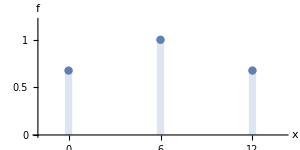

```mathematica
discreteExample=DiscretePlot[
	f2[i],{i,0,12,6}, 
	ExtentSize->Scaled[0.08],
	PlotMarkers->Point,
	PlotStyle->PointSize[0.02], 
	PlotRange->{{-2,14},{0,1.2}},
	Ticks->{{0,6,12},{0,0.5,1}},
	TicksStyle->18,
	AxesLabel->{"x","f"},
	LabelStyle->20,
	ImageSize->300,
	AspectRatio->0.5
]
```

```mathematica
Export["../TeX/Slike/discreteExample.png", discreteExample,ImageResolution->90]
```

../TeX/Slike/discreteExample.png

```mathematica
Table[Round[f2[i],0.01],{i,0,12,1}]
```

{0.68,0.76,0.84,0.91,0.96,0.99,1.,0.99,0.96,0.91,0.84,0.76,0.68}

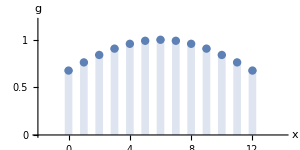

```mathematica
discreteExample2=DiscretePlot[
	f2[i],{i,0,12,1}, 
	ExtentSize->Scaled[0.5],
	PlotMarkers->Point,
	PlotStyle->PointSize[0.02], 
	PlotRange->{{-2,14},{0,1.2}},
	Ticks->{{0,2,4,6,8,10,12},{0,0.5,1}},
	TicksStyle->18,
	AxesLabel->{"x","g"},
	LabelStyle->20,
	ImageSize->300,
	AspectRatio->0.5
]
```

```mathematica
Export["../TeX/Slike/discreteExample2.png", discreteExample2,ImageResolution->90]
```

../TeX/Slike/discreteExample2.png

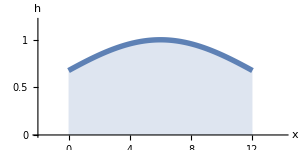

```mathematica
discreteExample3=Plot[
	f2[x],{x,0,12},
	PlotStyle->Thickness[0.013],
	Filling->Bottom,
	PlotRange->{{-2,14},{0,1.2}},
	Ticks->{{0,2,4,6,8,10,12},{0,0.5,1}},
	TicksStyle->18,
	AxesLabel->{"x","h"},
	AxesOrigin->{-2,0},
	LabelStyle->20,
	ImageSize->300,
	AspectRatio->0.5
]
```

```mathematica
Export["../TeX/Slike/discreteExample3.png", discreteExample3,ImageResolution->90]
```

../TeX/Slike/discreteExample3.png

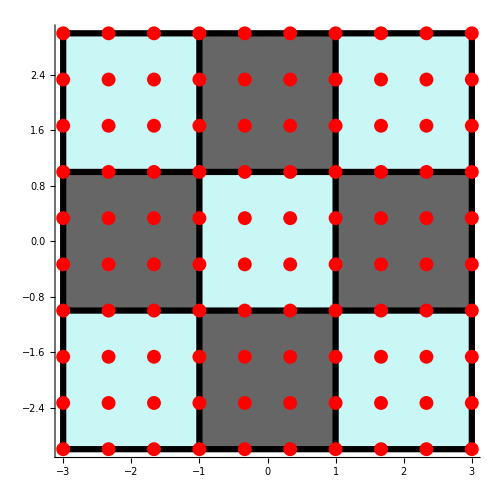

```mathematica
layout2d=Graphics[
	{
		RGBColor["#a4f2f1"], Opacity[0.6],
		lightSquares,
		Black,
		darkSquares,
		Thickness[0.009],Opacity[1.0],
		lines,
		Red,PointSize[0.02],
		Point[Flatten[nodes,1]]
	},
	Axes->True,
	AxesOrigin->{-3.2,-3.2},
	AxesStyle->Directive[26, Black],
	ImageSize->500
]
```

```mathematica
Export["../TeX/Slike/layout2d.png", layout2d,ImageResolution->90]
```

layout2d.png

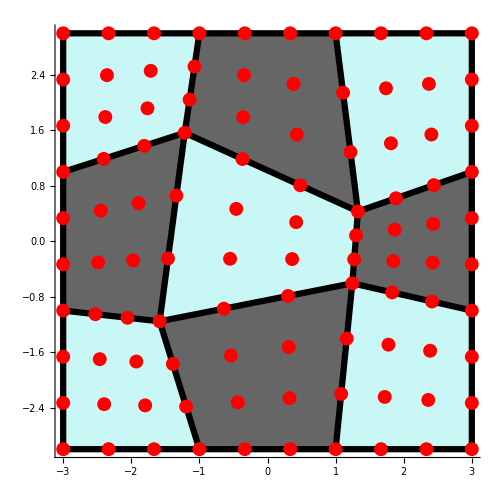

```mathematica
layout2dTrans=Graphics[
	{
		RGBColor["#a4f2f1"], Opacity[0.6],
		transLightSquares,
		Black,Thickness[0.009],
		transDarkSquares,
		Opacity[1],
		transLines,
		Red,PointSize[0.02],
		Point[Flatten[transNodes,1]]
	},
	Axes->True,
	AxesOrigin->{-3.2,-3.2},
	AxesStyle->Directive[26, Black],
	ImageSize->500
]
```

```mathematica
Export["layout2dTrans.png", layout2dTrans,ImageResolution->90]
```

layout2dTrans.png